```mathematica
(*Ćwiczenie 2.:
  1. Wykorzystując np.program Mathematica wyznaczyć datę Wielkanocy w 2023 roku
korzystając z algorytmu Meeusa dla kalendarza gregoriańskiego.
2. Przygotuj odpowiednie zestawienie w formie np.list wyników tego wydarzenia za
okres od 2000 do 2050 roku.Wykorzystując dowolny program przedstaw wykres np.słupkowy ile raz Wielkanoc wystąpi w marcu a ile razy w kwietniu.*)
```

```mathematica
a=Mod[2023,19];
b=Floor[2023/100];
c=Mod[2023,100];
d=Floor[b/4];
e=Mod[b,4];
f=Floor[(b+8)/25];
g=Floor[(b-f+1)/3];
h=Mod[(19 a+b-d-g+15),30];
i=Floor[c/4];
k=Mod[c,4];
l=Mod[(32+2 e+2 i-h-k),7];
m=Floor[(a+11 h+22 l)/451];
p=Mod[(h+l-7 m+114),31];

day=p+1;
month=Floor[(h+l-7 m+114)/31];

Print["Data Wielkanocy w 2023 roku to ",day," ",month]
```

Data Wielkanocy w 2023 roku to 9 4

{{2000,4,23},{2001,4,15},{2002,3,31},{2003,4,20},{2004,4,11},{2005,3,27},{2006,4,16},{2007,4,8},{2008,3,23},{2009,4,12},{2010,4,4},{2011,4,24},{2012,4,8},{2013,3,31},{2014,4,20},{2015,4,5},{2016,3,27},{2017,4,16},{2018,4,1},{2019,4,21},{2020,4,12},{2021,4,4},{2022,4,17},{2023,4,9},{2024,3,31},{2025,4,20},{2026,4,5},{2027,3,28},{2028,4,16},{2029,4,1},{2030,4,21},{2031,4,13},{2032,3,28},{2033,4,17},{2034,4,9},{2035,3,25},{2036,4,13},{2037,4,5},{2038,4,25},{2039,4,10},{2040,4,1},{2041,4,21},{2042,4,6},{2043,3,29},{2044,4,17},{2045,4,9},{2046,3,25},{2047,4,14},{2048,4,5},{2049,4,18},{2050,4,10}}

{{2002,3,31},{2005,3,27},{2008,3,23},{2013,3,31},{2016,3,27},{2024,3,31},{2027,3,28},{2032,3,28},{2035,3,25},{2043,3,29},{2046,3,25}}

{{2000,4,23},{2001,4,15},{2003,4,20},{2004,4,11},{2006,4,16},{2007,4,8},{2009,4,12},{2010,4,4},{2011,4,24},{2012,4,8},{2014,4,20},{2015,4,5},{2017,4,16},{2018,4,1},{2019,4,21},{2020,4,12},{2021,4,4},{2022,4,17},{2023,4,9},{2025,4,20},{2026,4,5},{2028,4,16},{2029,4,1},{2030,4,21},{2031,4,13},{2033,4,17},{2034,4,9},{2036,4,13},{2037,4,5},{2038,4,25},{2039,4,10},{2040,4,1},{2041,4,21},{2042,4,6},{2044,4,17},{2045,4,9},{2047,4,14},{2048,4,5},{2049,4,18},{2050,4,10}}

11

40

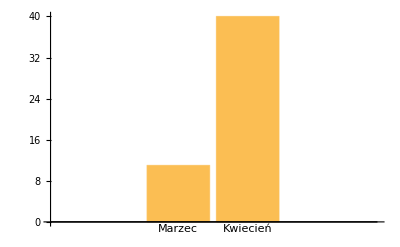

```mathematica
easterDates=Table[EasterSunday[i],{i,2000,2050}]
marchEasters=Cases[easterDates,d_/;DateValue[d,"Month"]==3]
aprilEasters=Cases[easterDates,d_/;DateValue[d,"Month"]==4]
numMarchEasters=Count[easterDates,d_/;DateValue[d,"Month"]==3]
numAprilEasters=Count[easterDates,d_/;DateValue[d,"Month"]==4]
BarChart[{numMarchEasters,numAprilEasters},ChartLabels->{"Marzec","Kwiecień"}]
```